# RABBIT: Reconstructing genome ancestry blocks in multiparental populations

## Chaozhi Zheng Biometris, Wageningen University and Research centre Dec 15, 2014

## Helps on “MagicReconstruct`”

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]<>"\\RABBIT_Packages"];
Needs["MagicReconstruct`"]
?"MagicReconstruct`*"
```

```mathematica
?magicReconstruct
```

magicReconstruct[magicSNP, model, epsF, eps, matingScheme, outputfile] reconstructs the ancestral origins in multi-parental populations. magicSNP is the input marker data, which are analyzed under the model using a HMM algorithm HMMMethod. The parameters epsF and eps refer to the allelic typing errors for founders and sampled individuals, respectively. The parameter matingScheme is a list of mating schemes of the mapping population until the last generation. The results are saved in outputfile. 
 magicReconstruct[magicSNPfile, model, epsF, eps, matingScheme, outfile] where the input marker data are privided as the filename magicSNPfile.

```mathematica
Options[magicReconstruct]
```

{HMMMethod→origPathSampling,SampleSize→1000,PrintTimeElapsed→False}

```mathematica
?HMMMethod
```

HMMMethod is an option to specify the alogrithm used for Hidden Markov Model, it has to be one of "origPathSampling", "origPosteriorDecoding", or "origViterbiDecoding".

## Example data: simulated CC

Consider two males and two females  are sampled independently from CC funnels at generation F11. The true allelic error probabilitis are 0.005 for both founders and samples. One pair of autosomes and One pair of sex chromosomes.

```mathematica
SetDirectory[NotebookDirectory[]];
magicSNP=Import["MagicReconstruct_Input_ExampleCC.csv"];
magicSNP[[1]]
magicSNP[[2;;, ;;;;Round[Last[Dimensions[Rest[magicSNP]]]/9]]]//TableForm
```

{#founders,8}

SNP | UNC011275068 | UNC011510234 | UNC010259898 | backuprs32565732 | JAX00709389 | UNC200093280 | UNC200108569 | UNC200036229 | JAX00187177
Chromosome | 1 | 1 | 1 | 1 | X | X | X | X | X
cM | 22.8 | 41.8223 | 64.1278 | 83.8805 | 6.12812 | 28.6456 | 46.7543 | 63.5105 | 82.6962
A/J | 1 | 2 | 1 | 2 | 1 | N | 1 | 1 | 2
C57BL/6J | 1 | 2 | 2 | 2 | 1 | N | 1 | 1 | 2
129S1/SvImJ | 1 | 2 | 1 | 2 | N | N | 1 | 2 | 1
NOD/ShiLtJ | 1 | 2 | 1 | 1 | 1 | N | 1 | 1 | 1
NZO/HlLtJ | 2 | 2 | N | 2 | N | 1 | 1 | 1 | 1
CAST/EiJ | 2 | 1 | 1 | 1 | N | 1 | 1 | 2 | 1
PWK/PhJ | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1
WSB/EiJ | 2 | 1 | 2 | 2 | N | 1 | 1 | 1 | 1
Line1 | 11 | 22 | 11 | 11 | 1 | N | 1 | 1 | 2
Line2 | 11 | 22 | 11 | 11 | 11 | 11 | 11 | 22 | 11
Line3 | 22 | 22 | NN | 22 | N | 1 | 1 | 1 | 1
Line4 | 11 | 12 | 11 | 11 | NN | 11 | 11 | 11 | 11

Input CSV formatted data

Row 1 species the number of founder strains

The rest shows as a matrix for genetic map and SNP data for founders and sampled individuals.

Let 1 and 2 denote the two alleles of SNPs, and N for missing alleles. The founders and male X chromosomes are shown as haplotypes.

## Estimate the sample generation

List of mating schemes, where each scheme refer to the lines being sampled from a single generation.  In prior, the candicate generations in the schemelist is equally probable.

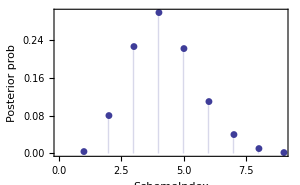
{SchemeIndex | PosteriorProb
4 | 0.300077
3 | 0.226962
5 | 0.222185
6 | 0.110438
2 | 0.0809439
7 | 0.0402059
8 | 0.0114429
1 | 0.00508275
9 | 0.00266335,-Graphics-}

```mathematica
schemelist=Table[Join[Table["Pairing",{2}],Table["Sibling",{i}]],{i,3,11}];
(*assuming all the sampled lines are from the same generation*)
issamegeneration =True; 
res=calOrigGeneration[magicSNP,model,epsF,eps,schemelist,issamegeneration];
{res//TableForm,ListPlot[res[[2;;]],ImageSize->300,PlotMarkers->Automatic,Filling->Axis,Frame->{{True,False},{True,False}},FrameLabel->{"SchemeIndex","Posterior prob"}]}
```

The estimated matingscheme is given as follow; the maxixum a posterior estimation is F8, different from the true F11, because of limited data.

```mathematica
schemelist[[res[[2,1]]]]
Length[%]
```

{Pairing,Pairing,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling}

8

## Posterior decoding

Set the input parameters: matingScheme, epsF, eps, model, inputfile, and outputfile.

```mathematica
matingScheme=Join[Table["Pairing",{2}],Table["Sibling",{9}]]
epsF=eps=0.005;
model="jointModel";
estfun="origPosteriorDecoding";
outputfile="MagicReconstruct_Output_ExampleCC_"<>model<>"_"<>estfun<>".txt"
inputfile="MagicReconstruct_Input_ExampleCC.csv"
```

{Pairing,Pairing,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling}

MagicReconstruct_Output_ExampleCC_jointModel_origPosteriorDecoding.txt

MagicReconstruct_Input_ExampleCC.csv

```mathematica
magicReconstruct[inputfile,model,epsF,eps,matingScheme,outputfile,HMMMethod->estfun,PrintTimeElapsed->True];
```

Start date =Tue 13 Jan 2015 14:51:54

Pre-computing data probability...	outputfile = MagicReconstruct_Output_ExampleCC_jointModel_origPosteriorDecoding.txt

Time elapsed = 0.6 Seconds.	Starting analyzing line 1 of 4

Time elapsed = 0.7 Seconds.	Starting analyzing line 2 of 4

Time elapsed = 0.7 Seconds.	Starting analyzing line 3 of 4

Time elapsed = 0.8 Seconds.	Starting analyzing line 4 of 4

Done! Finished date =Tue 13 Jan 2015 14:51:55. 	Time used in total = 0.9 Seconds.

## Conidtional posterior probability

Summary the output of magicReconstruct.

```mathematica
resultFile="MagicReconstruct_Output_ExampleCC_jointModel_origPosteriorDecoding.txt"; summaryFile=StringDrop[resultFile,-4]<>"_Summary.csv"; saveAsSummaryMR[resultFile,summaryFile];res=getSummaryMR[summaryFile];First[res]//TableForm
```

MagicReconstruct-Summary | Genetic map of biallelic markers
MagicReconstruct-Summary | Ln marginal likelihood
MagicReconstruct-Summary | Genotypes in order
MagicReconstruct-Summary | Conditonal genotype probability
MagicReconstruct-Summary | haplotypes in order
MagicReconstruct-Summary | Conditonal haplotype probability

Posterior genotype porbabilities at markers of each sampled lines.

```mathematica
types=origGenotypes[8];
truegeno=ToExpression[Import["MagicReconstruct_TrueDiplotype_ExampleCC.csv"][[4;;,2;;]]];
truegeno=(truegeno/.Thread[types[[1,2]]->Range[Length[types[[1,2]]]]])/.Thread[Range[Length[types[[2,2]]]]->types[[2,2]]];
gggenoprob=Table[
pos=Span@@{4+36 (line-1),3+36 line};
condprob=res[[5,pos,2;;]];
Show[
MatrixPlot[Reverse[condprob],FrameLabel->{"Genotypes","SNP"},ColorFunctionScaling->False,MaxPlotPoints->Infinity,AspectRatio->1/2.5,DataRange->{{1,Dimensions[condprob][[2]]},{1,Length[condprob]}}],
ListPlot[Transpose[{Range[Length[truegeno[[line]]]],truegeno[[line]]}],PlotRange->{{1,Dimensions[condprob][[2]]},{1,Length[condprob]}},PlotRangePadding->0,PlotMarkers->{"×",10},PlotStyle->Red],
ListLinePlot[Thread[{Count[res[[5,2,2;;]],res[[5,2,2]]],{1,Length[condprob]}}],PlotStyle->{Dashed,Thick}],
FrameTicks->{{Transpose[{Range[Length[types[[1,1]]]],types[[1,1]]}],None},{Automatic,None}},
ImageSize->900,Frame->True,PlotLabel->"Line "<>ToString[line]<>". GrayLevel=Posterior Probability, red X=True Genotype."
],{line,Length[truegeno]}];
ListAnimate[gggenoprob]
```

## Viterbi decoding

Estimate the optimal sequences by viterbi decoding and summary the output.

```mathematica
model="jointModel"; 
estfun="origViterbiDecoding";outputfile="MagicReconstruct_Output_ExampleCC_"<>model<>"_"<>estfun<>".txt";
magicReconstruct[inputfile,model,epsF,eps,matingScheme,outputfile,HMMMethod->estfun,PrintTimeElapsed->True];
```

Start date =Tue 13 Jan 2015 14:51:58

Pre-computing data probability...	outputfile = MagicReconstruct_Output_ExampleCC_jointModel_origViterbiDecoding.txt

Time elapsed = 0.6 Seconds.	Starting analyzing line 1 of 4

Time elapsed = 0.9 Seconds.	Starting analyzing line 2 of 4

Time elapsed = 1.5 Seconds.	Starting analyzing line 3 of 4

Time elapsed = 1.9 Seconds.	Starting analyzing line 4 of 4

Done! Finished date =Tue 13 Jan 2015 14:52:00. 	Time used in total = 2.5 Seconds.

```mathematica
resultFile=outputfile; summaryFile=StringDrop[resultFile,-4]<>"_Summary.csv"; 
saveAsSummaryMR[resultFile,summaryFile]
res=getSummaryMR[summaryFile];First[res]//TableForm
```

MagicReconstruct_Output_ExampleCC_jointModel_origViterbiDecoding_Summary.csv

MagicReconstruct-Summary | Genetic map of biallelic markers
MagicReconstruct-Summary | Ln marginal likelihood
MagicReconstruct-Summary | haplotypes in order
MagicReconstruct-Summary | diplotypes in order
MagicReconstruct-Summary | Viterbi path of diplotypes

## Viterbi path

Viterbi path (tranformed from diplotypes into genotypes) at markers for each sampled lines.

```mathematica
ggviterbi=Table[
path=Flatten[Map[CtDiscreteFormat[CtJumpFormat[#]]&,StringSplit[res[[6,line+1,2]],"||"]]]/.Thread[Range[Length[types[[2,2]]]]->types[[2,2]]];
ListLinePlot[Transpose[{Range[Length[path]],path}],PlotRange->{{1,Dimensions[condprob][[2]]},{1,Length[condprob]}},PlotRangePadding->0,PlotStyle->Blue,PlotStyle->{Thick}],{line,Length[res[[6]]]-1}];
gg=Table[Show[gggenoprob[[line]],ggviterbi[[line]],PlotLabel->"Line "<>ToString[line]<>". GrayLevel=Posterior Probability, red X=True Genotype, blue line = Viterbi path"],{line,Length[ggviterbi]}];
ListAnimate[gg]
```

## Posterior sampling

Posterior sampling and summary the output.

```mathematica
model="jointModel";  estfun="origPathSampling";
outputfile="MagicReconstruct_Output_ExampleCC_"<>model<>"_"<>estfun<>".txt";
magicReconstruct[inputfile,model,epsF,eps,matingScheme,outputfile,HMMMethod->estfun,SampleSize->20,PrintTimeElapsed->True];
```

Start date =Tue 13 Jan 2015 14:52:02

Pre-computing data probability...	outputfile = MagicReconstruct_Output_ExampleCC_jointModel_origPathSampling.txt

Time elapsed = 0.6 Seconds.	Starting analyzing line 1 of 4

Time elapsed = 0.7 Seconds.	Starting analyzing line 2 of 4

Time elapsed = 0.7 Seconds.	Starting analyzing line 3 of 4

Time elapsed = 0.8 Seconds.	Starting analyzing line 4 of 4

Done! Finished date =Tue 13 Jan 2015 14:52:02. 	Time used in total = 0.9 Seconds.

```mathematica
resultFile=outputfile; summaryFile=StringDrop[resultFile,-4]<>"_Summary.csv"; 
saveAsSummaryMR[resultFile,summaryFile]
res=getSummaryMR[summaryFile];First[res]//TableForm
```

MagicReconstruct_Output_ExampleCC_jointModel_origPathSampling_Summary.csv

MagicReconstruct-Summary | Genetic map of biallelic markers
MagicReconstruct-Summary | Ln marginal likelihood
MagicReconstruct-Summary | haplotypes in order
MagicReconstruct-Summary | diplotypes in order
MagicReconstruct-Summary | Sampled paths of diplotypes

## Sampled path

20 randomly sampled path (tranformed from diplotypes into genotypes) at markers for line 1.

```mathematica
line=1;
paths=Flatten[#]&/@Map[CtDiscreteFormat[CtJumpFormat[#]]&,StringSplit[#,"|"]&/@StringSplit[res[[6,line+1,2]],"||"],{2}];
paths=paths/.Thread[Range[Length[types[[2,2]]]]->types[[2,2]]];
ggpaths=Table[
g=ListLinePlot[Transpose[{Range[Length[path]],path}],PlotRange->{{1,Dimensions[condprob][[2]]},{1,Length[condprob]}},PlotRangePadding->0,PlotStyle->Blue,PlotStyle->{Thick}];
g=Show[gggenoprob[[line]],g,PlotLabel->"Line "<>ToString[line]<>". GrayLevel=Posterior Probability, red X=True Genotype, blue line = Random sampled path"],{path,paths}];
ListAnimate[ggpaths]
```

## matingScheme for mapping populaitons

RABBIT requires matingScheme for the mapping population, and it is specified by a list with ith (i = 1, ...) elemnt being the mating scheme producing the F_i (t=i) population. The founder population F_0 (t=0) consists of L inbred founders.

Consider mapping populaitons with three stages: mixing, intercross, and inbreeding.  The mixing stage consist of only one generation F1,  the intercross states consists of U generations from F2 to F(U+1), and the inbreeding stage consists of V generations from F(U+2) to F(U+V+1).

Population type | #inbred founders L  | matingScheme  (e.g. U=2, V=2)
CC (one funnel) | 8 | {Pairing,Pairing, Sibling,Sibling}, U=1 fixed by L
MAGIC | 19 | {FullDiallel,RM1-E,RM1-E, Selfing,Selfing}
AIL | 2 | {RM1-NE-100,RM1-E,RM1-E,Selfing,Selfing}
HS | 8 | {Pairing,Pairing,Pairing, Pairing,RM1-E, RM1-E,RM1-E,Sibling,Sibling}
DSPR (one population) | 8 | {RM1-NE-500, RM1-E,RM1-E, Sibling,Sibling}
APRIL (4-way RIL) | 4 | {Pairing,Pairing, Selfing,Selfing}, U=1 fixed by L
Usered defined | 8 | {Pairing,RM1-E,RM1-E,Pairing,Sibling,Sibling,Pairing, Selfing,Selfing}

“Selfing” and “Sibling” (mating) are the mating schemes for inbreeding stage to obtain homozygous lines. “Pairing” refers to exclusively pairingwise mating and each pair produce one offspring so that the population size descreases by half.

Random mating schemes can be choose from  “RM1-E”, “RM1-NE”, “RM2-E”, and “RM2-NE” where the population size is maitained constant. To change the populaiton size, “RM1-NE-N” or “RM2-NE-N” may be used so that the produced populaiton has size N.

Warning:  the populaiton size is automatically determined by L  and matingScheme, and the user has to asssure that the resulting population size is correct.

## Refereces

Zheng, C., Boer, M. P., and Eeuwijk, F. A. 2014. Reconstruction of genome ancestry blocks in multiparental populations. Submitted.

Zheng, C. 2014. Modeling X-linked ancestral origins in multiparental populations. Submitted.

Zheng, C., Boer, M. P., and Eeuwijk, F. A. 2014. A general modeling framework for genome ancestral origins in multi-parental populations. Genetics. 198: 87-101.